## Theory

The spontaneous emission rate for photons of a given momentum k from a QGP (at “high enough temperature”) is defined as ν_e(k)=(2π)^3 dΓ_γ/(d^3 k) . The AMY formalism allows to evaluate ν_e(k) at full leading order in α_EM and g_s(T), under a certain number of assumptions [1].

The formula for ν_e(k) in AMY is:

ν_e(k)=A(k) ∫_(-∞)^∞ ⅆp_‖[((p_‖)^2+(p_‖+k)^2)/(4 ((p_‖)^2(p_‖+k))^2)] (n_f(k+p_‖) (1-n_f(p_‖)))/(m_∞^2 n_f(k))∫(ⅆ^2 p_T)/(2π)^2 Re[2p_T·f(p_T,p_‖,k)]

where f(p_T,p_‖,k) is given by the integral equation

2 p_T=i δE(p_T) f(p_T,p_‖,k) +g_s^2 C_F T∫(ⅆ^2 q_T)/(2π)^2 C(q_T)[f(p_T,p_‖,k)-f(p_T+q_T,p_‖,k)]

A (k), n_f(k), δE(p) and C(q) are given by:

A (k)=2 α_EM(d_F∑_(s=1)^N_F q_s^2)(m_∞^2)/k n_f(k)

n_f(k)=1/(e^(k/T)+1)

δE(p)=k/(2 p_‖(k+p_‖))[p^2+m_∞^2]+m_γ^2/(2k)=μ p^2+μ M_eff^2; μ=k/(2 p_‖(k+p_‖)); M_eff^2= m_∞^2+m_γ^2/(2k μ)

C(q)=(1/q^2-1/(q^2+m_D^2))       (the definition of C(q) differs from paper to paper as various factors are sometimes included)

The analytical solution of (eq. 2) is not known. A fairly straightforward way of solving (eq. 2) numerically is described in [2] (another is described in [1]). The idea is that in position space, (eq. 2) is a differential equation from which the integral ∫(ⅆ^2 p_T)/(2π)^2 Re[2p_T·f(p_T,p_‖,k)]  can be calculated in a straightforward way. The details are in [2], but here are the main steps.

By inverse-Fourier-transforming (eq. 2) and taking f(b,p_‖,k)=b h(b,p_‖,k)  (this is justified by rotational invariance in the transverse plane, whatever this means), one gets the ordinary differential equation (it is unclear how the small b dependence is obtained)

i μ(M_eff^2-∂_b^2 -(3∂_b)/b)h(b)+g_s^2 C_F T D(m_D b)h(b)=0; h(b→∞)=0; h(b→0^+)≈1/(π μ b^2)+K     (K is unknown)

where

D(x)=1/(2π)(γ_E+ln(x/2)+K_0(x))             (An easy way to get this expression for D(x) is to replace C(q) by (C(q))^(1+ϵ) and take ϵ→0 at the end )

The beauty of this is that ∫(ⅆ^2 p_T)/(2π)^2 Re[2p_T·f(p_T,p_‖,k)] = 4 Limit[Im[h(b)],b→0^+]

[1] P. Arnold, G. D. Moore and L. G. Yaffe. “Photon emission from quark-gluon plasma: complete leading order results”, JHEP 12, 009 (2001)
[2] P. Aurenche, F. Gelis, G. D. Moore and H. Zaraket, “Landau-Pomeranchuk-Migdal resummation for dilepton production”, JHEP 12, 006 (2002)

## Preliminary manipulations

It is convenient (compulsory if numerical, as opposed to symbolic, calculations are involved) to strip the units of every variable.

m_D=mDt T
m_∞=mInft T
m_γ=mGammat T
μ=mut/T
M_eff=Mefft T
b=x/T

where all the new variables are unitless.

Thus, (eq. 3) becomes

i mut (Mefft^2-∂_x^2 -(3∂_x)/x)f(x)+g_s^2 C_F D(mDt x)f(x)=0; f(x→∞)=0; f(x→0^+)≈1/(π mut x^2)+Kb ; h(x T)=T^3 f(x); K=T^3 Kb

It is then assumed that k, p_‖ and T are given in some unit U (GeV being the sensible choice):

k=ku U
p_‖=pu U
T=Tu U

ν_e(k) is thus become

ν_e(k)=U Au(k) ∫_(-∞)^∞ ⅆpu ((pu^2+(pu+ku)^2)/(4(pu^2(pu+ku))^2)) (n_f(ku+pu) (1-n_f(pu)))/(mInft^2 Tu^2 n_f(ku))(4 Tu^3 Limit[Im[f(x)],x→0^+]);       A(k)=Au(k) U;  Au(k)=2α_EM(d_F∑_(s=1)^N_F q_s^2)(Tu^2 mInft^2)/ku n_f(ku)

## Parameters

Every parameter except k (ku) (excluding new numerical parameters, on which the results should not depend) are set here. Beware that there is a significant difference in Mathematica between using e.g. 1 (symbol for 1) and 1. (which is interpreted as the floating point representation of 1 to some precision). As numerical functions are used below (NDSolve, NIntegrate, ...), it is pointless, and above all much slower, to force Mathematica to use symbols here.

```mathematica
ClearAll["Global*"]
```

ClearAll::wrsym: Symbol GlobalClusteringCoefficient is Protected.

ClearAll::wrsym: Symbol GlobalPreferences is Protected.

ClearAll::wrsym: Symbol GlobalSession is Protected.

General::stop: Further output of ClearAll::wrsym will be suppressed during this calculation.

```mathematica
(* Number of colors *)
Nc=3;
(* Temperature in units of U *)
Tu=.25;
(* Strong coupling constant *)
gs=Sqrt[4Pi(3./10)];
(* Electromagnetic coupling constant *)
ge=Sqrt[4Pi/137];
```

```mathematica
(* Temperature-stripped Debye mass *)
mDt[Nf_]:=gs Sqrt[(1+Nf/6)];
(* Temperature-stripped Debye mass *)
mInft:=gs/Sqrt[3];
(* Temperature-stripped thermal mass *)
mGammat[Nf_]:=1/Sqrt[2]*ge*Sqrt[Switch[Nf,1,(2/3)^2,2,(2/3)^2+(1/3)^2,3,(2/3)^2+2(1/3)^2,4,2(2/3)^2+2(1/3)^2,5,2(2/3)^2+3(1/3)^2,6,3(2/3)^2+3(1/3)^2]];
(* Temperature-stripped μ(pT,kT) *)
mut[pt_,kt_]:=Tu kt/2/pt/(kt+pt)
(* Temperature-stripped Subscript[M, eff]^2 *)
Mefft[Nf_,pt_,kt_]:=Sqrt[mInft^2+mGammat[Nf]^2 Tu/2/mut[pt,kt]/kt];
```

## Exact solution

```mathematica
(* Definition of D(x) *)
Dw[x_]:=(EulerGamma+Log[x/2]+BesselK[0,x])/(2 Pi)
```

```mathematica
(* Eq. 4, just for information, not used in calculations *)
```

```mathematica
I mut[pt,kt] (Mefft[Nf,pt,kt ]^2 h[x]-D[h[x],x,x]-3/x D[h[x],x])+4 gs^2  Dw[mDt[Nf] x] h[x]/3==0
```

0.8 h[x] (EulerGamma+BesselK[0,1.94163 √(1+Nf/6) x]+Log[0.970813 √(1+Nf/6) x])+((0.+0.125 ⅈ) kt (h[x] (1.25664+(0.0458627 pt (kt+pt) Switch[Nf,
1,(2/3)^2,
2,(2/3)^2+(1/3)^2,
3,(2/3)^2+2 (1/3)^2,
4,2 (2/3)^2+2 (1/3)^2,
5,2 (2/3)^2+3 (1/3)^2,
6,3 (2/3)^2+3 (1/3)^2])/kt^2)-(3 h'[x])/x-h''[x]))/(pt (kt+pt))==0

## Numerical LPM

The function fmod[] solves (eq. 4) and returns (4 Tu^3 Limit[Im[f(x)],x→0^+]). It does that by first finding a large-x solution for f(x). Then the first boundary condition (f(x→∞)=0) is applied. As the large-x solution for f(x) is an exponential, the remaining boundary conditions serves to fix the normalisation of that solution. Starting at a given large x (variable “xmb”), the large-x solution is then numerically evolved toward x→0, where the behaviour is known (f(x→0^+)≈1/(π mut x^2)+Kb ). That second “boundary condition” is used to find the normalisation and Kb at the same time. Since Limit[Im[f(x)],x→0^+]=Im[Kb], the relevant information contained in (eq. 4) is thus extracted.

```mathematica
fmod[Nf_?NumericQ,pt_?NumericQ,kt_?NumericQ]:=( 
(* Set the normalisation of the large-x solution to an arbitrary number *)
B=1;
(* Numerical parameter. Value at which the numerical evolution toward 0 will start. *)
xmb=5;
(* We never actually reach 0 as f(x) is singular at this point. This sets a low-enough value *)
lowbnd=10^-10;
(* Numerical parameter. Mathematica _tries_ to solve the differential equation with a relative error 10^precisiongoal. Of course, error estimation is not an exact science *)
precisiongoal=7;
(* Find the _exact_ large-x solution, to avoid having to introduce another numerical parameter *)
tmpres=((h[x]/.DSolve[I mut[pt,kt] (Mefft[Nf,pt,kt]^2 h[x]-D[h[x],x,x])+4 gs^2  Dw[mDt[Nf] xmb] h[x]/3==0,h[x],x,GeneratedParameters->C][[1]])/.{C[1]->0,C[2]->1});
If[Norm[tmpres/.x->1]>Norm[tmpres/.x->2],tmpres=1/tmpres];
(* Define the large-x solution *)
asympsol2[y_]:=B(tmpres/.x->y);
(* Define the derivative of the large-x solution *)
dasympsol2[y_]:=(D[asympsol2[x],x]/.x->y);
(* List of values that will be used as small number (10^-(those numbers)) when applying the second "boundary condition" *)
smallxlist={{3,6},{4.1,7.2},{4.8,7.354},{3,5},{4,6}};
Blist={};
Klist={};
(* The application of the second "boundary condition" numerically is tricky. The stability of the procedure is thus checked by repeating the process for various small numbers *)
Do[
(* Solve the full differential equation using the large-x solution to set the boundary conditions at the large-x value "xmb" *)
tmpres2=NDSolve[{I mut[pt,kt] (Mefft[Nf,pt,kt]^2 h[x]-D[h[x],x,x]-3/x D[h[x],x])+4 gs^2  Dw[mDt[Nf] x] h[x]/3==0,h[xmb]==N[asympsol2[xmb]],h'[xmb]==N[dasympsol2[xmb]]},h[x],{x,lowbnd,xmb},PrecisionGoal->precisiongoal,AccuracyGoal->Infinity][[1]];
numsol2[y_]:=(h[x]/.tmpres2)/.{x->y};
(* Two small values at which the second "boundary condition" is applied *)
smallx1=10^-(smallxlist[[j,1]]);
smallx2=10^-(smallxlist[[j,2]]);
(* Close to 0, f(x) ~ 1/(Pi x^2 mut)+Kb. However, our solution is not correctly normalised *)
(* Taking {B*f[smallx1]=1/(Pi smallx1^2 mut)+Kb,B*f[smallx2]=1/(Pi smallx2^2 mut)+Kb} and solving for Kb and the normalisation B yields the equations below *)
(* Remember that Im[Kb] is what we are solving for *)
B=B*-((smallx1^2-smallx2^2)/(π smallx1^2 smallx2^2 mut[pt,kt] (numsol2[smallx1]-numsol2[smallx2])));
K=-((smallx1^2 numsol2[smallx1]-smallx2^2 numsol2[smallx2])/(π smallx1^2 smallx2^2 mut[pt,kt] (numsol2[smallx1]-numsol2[smallx2])));
(* Store B and Im[K] and loop *)
Blist=Append[Blist,B];
Klist=Append[Klist,Im[K]]
(* Loop a certain number of time, at most Length[smallxlist] *)
,{j,1,5}];
(* Quick checks to assess the stability of the procedure (not sure how good these checks are) *)
If[MeanDeviation[Blist]/Norm[Mean[Blist]]<10^-3,check1=True;
If[(MeanDeviation[Klist]/Norm[Mean[Klist]]<10^-3),check2=True,check2=False];
,check1=False];
If[check1&&check2,Return[(4 Tu^3)Mean[Klist]],Return[NaN]];
)
```

```mathematica
(*With[{Nf=4,kt=15,pt=30},kt^4fmod[Nf,pt-kt,kt]]*)
```

```mathematica
(* Fermi-Dirac and Bose-Eistein distribution *)
nf[pu_]:=1/(Exp[pu/Tu]+1)
nb[pu_]:=1/(Exp[pu/Tu]-1)
```

```mathematica
(*FullSimplify[(pu^2+(pu+ku)^2)/(4 pu^2 (pu+ku)^2) nf[ku+pu](1-nf[pu])/nf[ku]]*)
```

((ku^2+2 ku pu+2 pu^2) Cosh[ku/(2 Tu)] Sech[pu/(2 Tu)] Sech[(ku+pu)/(2 Tu)])/(8 pu^2 (ku+pu)^2)

CbaIntegrand[Nf, ku, pu] returns the integrand of ∫_(-∞)^∞ ⅆp_‖[((p_‖)^2+(p_‖+k)^2)/(4 ((p_‖)^2(p_‖+k))^2)] (n_f(k+p_‖) (1-n_f(p_‖)))/(m_∞^2 n_f(k))∫(ⅆ^2 p_T)/(2π)^2 Re[2p_T·f(p_T,p_‖,k)] while Cba[Nf,ku,dku] returns the value of integral

```mathematica
CbaIntegrand[Nf_?NumericQ,ku_?NumericQ,pu_?NumericQ]:=((ku^2+2 ku pu+2 pu^2) Cosh[ku/(2 Tu)] Sech[pu/(2 Tu)] Sech[(ku+pu)/(2 Tu)])/(8 pu^2 (ku+pu)^2)fmod[Nf,pu,ku]/(mInft^2 Tu^2)
```

```mathematica
(*With[{Nf=3,ku=1.2,pu=56.56},CbaIntegrand[Nf,ku,pu-ku]]*)
```

```mathematica
(* CbaIntegrand[Nf,ku,pu] have singularities around pu=-ku and ku=0. Cba[Nf,ku,dku] does not integrate over a range "dku" around those points *)
```

```mathematica
Cba[Nf_?NumericQ,ku_?NumericQ,dku_?NumericQ]:=(NIntegrate[CbaIntegrand[Nf,ku,pu],{pu,-Infinity,-ku-dku},PrecisionGoal->3]+
NIntegrate[CbaIntegrand[Nf,ku,pu],{pu,-ku+dku,-dku},PrecisionGoal->3]+
NIntegrate[CbaIntegrand[Nf,ku,pu],{pu,dku,Infinity},PrecisionGoal->3])
```

```mathematica
(* As defined in [1], C_{tot}(k/T)=ln(2k/T)/2+C_{2->2}(x)+C_{brem}(x)+C_{annih}(x), which is related to Subscript[ν, e](k) by Subscript[ν, e](k)=A(k)*(ln(T/m_{inf})+C_{tot}(k/T))  *)
```

```mathematica
Ctot[Nf_,ku_,dku_]:=Cba[Nf,ku,dku]+C22[ku]+Log[2 ku/Tu]/2
```

```mathematica
(* FacA[Nf,ku] is Au(k), that is A(k) in the units chosen for T, k and p *)
FacA[Nf_,ku_]:=2 (ge^2/4/Pi) (Nc Switch[Nf,1,(2/3)^2,2,(2/3)^2+(1/3)^2,3,(2/3)^2+2(1/3)^2,4,2(2/3)^2+2(1/3)^2,5,2(2/3)^2+3(1/3)^2,6,3(2/3)^2+3(1/3)^2] ) mInft^2 (Tu^2)/ku nf[ku]
```

```mathematica
(* Finally, Emission[Nf,ku,dku] is Subscript[ν, e](k) in the units chosen for T, k and p *)
Emission[Nf_?NumericQ,ku_?NumericQ,dku_?NumericQ]:=FacA[Nf,ku] (Log[Sqrt[3]/gs]+Ctot[Nf,ku,dku])

(* Everything so far is brehmsstrahlung + pair annihilation *)
```

## Numerical 2 -> 2

12,5
As described in section 5 of [1], these are other contributions to the leading-order photon production of a QGP.
I_1=1/(2 π^2 T^2)∫_k^∞ ⅆω∫_(|2k-ω|)^ω ⅆq/q^2∫_((ω-q)/2)^((ω+q)/2) ⅆp (n_f(p)n_b(ω-p)(1-n_f(ω-k)))/(k n_f(k))(q^2-(2p-ω)(2k-ω))
I_2=1/(2 π^2 T^2)∫_(q_*)^∞ ⅆq/q^2∫_-q^(min(q,2k-q)) ⅆω∫_((ω+q)/2)^∞ ⅆp {(n_f(k-ω)n_b(p)(1-n_f(p-ω)))/(k n_f(k))((2k-ω)(2p-ω)+q^2)+(n_f(k-ω)n_f(p)(1+n_b(p-ω)))/(k n_f(k))((2k-ω)(2p-ω)-q^2)}
which can be rewritten in the unitless integrals
I_1=1/(2 π^2 Tu^2)∫_ku^∞ ⅆwu ∫_(|2ku-wu|)^wu ⅆqu/qu^2∫_((wu-qu)/2)^((wu+qu)/2) ⅆpu (n_f(pu)n_b(wu-pu)(1-n_f(wu-ku)))/(ku n_f(ku))(qu^2-(2pu-wu)(2ku-wu))
I_2=1/(2 π^2 Tu^2)∫_(qu_*)^∞ ⅆqu/qu^2∫_-qu^(min(qu,2ku-qu)) ⅆwu ∫_((wu+qu)/2)^∞ ⅆpu {(n_f(ku-wu)n_b(pu)(1-n_f(pu-wu)))/(ku  n_f(ku))((2ku-wu)(2pu-wu)+qu^2)+(n_f(ku-wu)n_f(pu)(1+n_b(pu-wu)))/(ku n_f(ku))((2ku-wu)(2pu-wu)-qu^2)}
The final formula is
C_(2⟷2)(k) =lim_(q_*→0) ( I_1(k)+I_2(k,q_*)+ln((q_*)/T)+1/2 ln((2T)/k)-1)

```mathematica
I1C22[ku_?NumericQ]:=1/(2Pi^2 Tu^2) NIntegrate[((4 ku pu-qu^2-2 (ku+pu) wu+wu^2) Cosh[ku/(2 Tu)] Csch[(pu-wu)/(2 Tu)] Sech[pu/(2 Tu)] Sech[(ku-wu)/(2 Tu)])/(4 ku qu^2),{wu,ku,Infinity},{qu,Abs[2 ku-wu],wu},{pu,(wu-qu)/2,(wu+qu)/2},PrecisionGoal->5,AccuracyGoal->Infinity]
I2C22[ku_?NumericQ,qsu_?NumericQ]:=1/(2 Pi^2 Tu^2) NIntegrate[(Cosh[ku/(2 Tu)] Csch[pu/Tu] Csch[(pu-wu)/Tu] Sech[(ku-wu)/(2 Tu)] (-(2 ku-wu) (-2 pu+wu) Sinh[(2 pu-wu)/(2 Tu)]-qu^2 Sinh[wu/(2 Tu)]))/(ku qu^2),{qu,qsu,Infinity},{wu,-qu,Min[{qu,2ku-qu}]},{pu,(qu+wu)/2,Infinity},PrecisionGoal->5,AccuracyGoal->Infinity]
I2C22lin[ku_?NumericQ,qsu_?NumericQ]:= 1/(2 Pi^2 Tu^2) NIntegrate[(Cosh[ku/(2 Tu)] Sech[(ku-wu)/(2 Tu)]Csch[pu/(2Tu)]Sech[(pu-wu)/(2Tu)] ((2 ku-wu) (2 pu-wu)+qu^2))/(4ku qu^2),{qu,qsu,Infinity},{wu,-qu,Min[{qu,2ku-qu}]},{pu,(qu+wu)/2,Infinity},PrecisionGoal->5,AccuracyGoal->Infinity]
I2C22quad[ku_?NumericQ,qsu_?NumericQ]:= 1/(2 Pi^2 Tu^2) NIntegrate[(Cosh[ku/(2 Tu)]  Sech[(ku-wu)/(2 Tu)] Sech[pu/(2Tu)]Csch[(pu-wu)/(2Tu)] ((2 ku-wu) (2 pu-wu)-qu^2))/(4ku qu^2),{qu,qsu,Infinity},{wu,-qu,Min[{qu,2ku-qu}]},{pu,(qu+wu)/2,Infinity},PrecisionGoal->5,AccuracyGoal->Infinity]
```

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
C22[ku_]:=NLimit[(I1C22[ku]+I2C22[ku,qsu]+(Log[qsu/Tu]+Log[2Tu/ku]/2-1)),qsu->0,Direction->-1,Method->SequenceLimit]
C22lin[ku_] := NLimit[(I1C22[ku]+I2C22lin[ku,qsu]+0.5*(Log[qsu/Tu]+Log[2Tu/ku]/2-1)),qsu->0,Direction->-1,Method->SequenceLimit]
C22quad[ku_] := NLimit[(I2C22quad[ku,qsu]+0.5*(Log[qsu/Tu]+Log[2Tu/ku]/2-1)),qsu->0,Direction->-1,Method->SequenceLimit]
```

## AMY fits

```mathematica
(* "Approximate, phenomenological fits" for C_{2->2}(x) and C_{brem}(x)+C_{annih}(x), as defined in [1] *)
```

```mathematica
ClpmAMY[Nf_,x_]:=Sqrt[1+Nf/6](.548Log[12.28+1/x]/x^(3/2)+.133x/Sqrt[1+x/16.27])
C22AMY[x_]:=(.041/x-.3615+1.01Exp[-1.35x])
```

```mathematica
(* C_{tot}(x) using the above approximate functions (and _not_ the numerical solution found in the previous section) *)
```

```mathematica
CtotAMY[Nf_,x_]:=ClpmAMY[Nf,x]+C22AMY[x]+Log[2 x]/2
```

## Numerical tests

```mathematica
(* Cba[Nf, ku, dku] should be very close to the approximation ClpmAMY[Nf,k/T], and should be very nearly independent of dku, as long as the latter is small enough *)
```

```mathematica
AMYres=ClpmAMY[2,10/Tu]
currentRes1=Cba[2,10,10^-2]
currentRes2=Cba[2,10,10^-3]
currentRes3=Cba[2,10,10^-4]
(AMYres-currentRes1)/AMYres*100
(AMYres-currentRes2)/AMYres*100
(AMYres-currentRes2)/AMYres*100
```

3.30949

3.33636

3.35083

3.35228

-0.811899

-1.24913

-1.24913

```mathematica
AMYres=ClpmAMY[2,10/Tu]
currentRes1=Cba[2,10,10^-2]
(AMYres-currentRes1)/AMYres*100
```

3.30949

3.33636

-0.811899

```mathematica
AMYres=ClpmAMY[2,.25/Tu]
```

1.78559

```mathematica
AMYres=ClpmAMY[2,.25/Tu]
```

1.78559

```mathematica
currentRes1=Cba[2,.25,10^-2]
```

1.71036

```mathematica
I2C22[1,1]
```

0.0880285

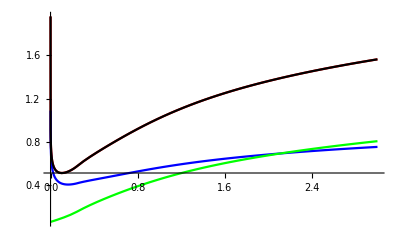

```mathematica
qval = 0.25;
plot1=Plot[I2C22[x,qval],{x,0,3},PlotStyle->Red];
plot2=Plot[I2C22lin[x,qval],{x,0,3},PlotStyle->Blue];
plot3=Plot[I2C22quad[x,qval],{x,0,3},PlotStyle->Green];
plot4=Plot[I2C22quad[x,qval]+I2C22lin[x,qval],{x,0,3},PlotStyle->Black];

Show[plot1,plot2,plot3,plot4,PlotRange->All,PlotLegends->{"I2C22","I2C22lin","I2C22quad","I2C22sum"}]
```

```mathematica
NIntegrate[Sin[x],{x,0,Pi},WorkingPrecision->MachinePrecision]

Options[NIntegrate]  (*Check updated options for NIntegrate*)
```

2.

{AccuracyGoal→∞,Compiled→Automatic,EvaluationMonitor→None,Exclusions→None,MaxPoints→Automatic,MaxRecursion→Automatic,Method→Automatic,MinRecursion→0,PrecisionGoal→Automatic,WorkingPrecision→MachinePrecision}

## Rate

```mathematica
Rate[qs_?NumericQ,Nf_?NumericQ,kt_?NumericQ,pt_?NumericQ]:=With[{x=kt/pt},kt^4(qs^2 ge^2)/(16 π pt^7) (1+(1-x)^2)/(x^3 (1-x)^2) fmod[Nf,pt-kt,kt]]
```

```mathematica
(* First generate table of Subscript[C, 2<->2] - swap lin <-> quad as needed *)
TuValues=Range[0.1,0.8,0.002];
kuValues = Range[0.05,4,0.05];

(* Large table, so this may take several hours *)
table=Table[Block[{Tu=TuVal},Table[C22lin[ku],{ku,kuValues}]],{TuVal,TuValues}];

N[table]
processedTable=table/.{expr_NLimit:>N[expr],(*Evaluate NLimit if possible*)expr_Symbol/;NumericQ[expr]:>N[expr]  (*Evaluate other expressions that are purely numerical*)};

(* Export the table to a text file *)
Export["output_lin.txt",processedTable,"Table"]
(* This is what agreed with the analytic fit *)
```

```mathematica
nf[Tu_,ku_]:=1/(Exp[ku/Tu]+1);
A[Tu_,ku_] :=  (40 Tu^2)/9 ge^2/(4 π) gs^2/4 nf[Tu,ku]/ku;
logTerms[Tu_,ku_] := 0.5*(Log[Sqrt[3]/gs] + Log[2 ku/Tu]/2); (* Factor of 1/2 in logTerms because it's added to both linear and quadratic *)
```

```mathematica
(* Read in the Subscript[C, 2<->2], add logarithmic terms, and multiply by A(k) *)
originalTable=Import["output_lin.txt","Table"];

modifiedTable=MapIndexed[A[TuValues[[#2[[1]]]],kuValues[[#2[[2]]]]]*(#1+logTerms[TuValues[[#2[[1]]]],kuValues[[#2[[2]]]]])&,originalTable,{2}];

(*Export the modified table to a new text file*)
Export["output_lin_modified.txt",modifiedTable,"Table"]

(* This generates the first version I showed - no powers of k or constants multiplied by the result *)
```

output_lin_modified.txt